## Set working directory

```mathematica
Off[General::spell1];
Off[General::spell];$HistoryLimit=0;
FilePath="E:\\Mathemetica";
SetDirectory[FilePath]
```

E:\Mathemetica

## General Function

### Rad To Deg (*自訂一個函式 徑度 轉 角度*)

```mathematica
RadToDeg[Rad_]:=Module[{deg},    
deg=Rad/π*180.0;
Return[deg];
];
```

# 1. Positions for a Four-Bar Mechanism

### Four-bar linkanges

## 1.1 Parameters

### Bar lengths

```mathematica
Subscript[l, 1]=40.0;
Subscript[l, 2];
Subscript[l, 3]=50.0;
Subscript[l, 4]=22.0;
Subscript[l, 5]=35.0;
Subscript[l, 6]=35.0;
Subscript[l, 7]=20.0;
```

### Angle 1、2

```mathematica
vtheta1=0;
vtheta2=π;
```

### Input Position

```mathematica
vl2=60.0; (*預設*)
```

### Link position

```mathematica
r1=Subscript[l, 1]*{Cos[Subscript[θ, 1]],Sin[Subscript[θ, 1]]};
r2=Subscript[l, 2]*{Cos[Subscript[θ, 2]],Sin[Subscript[θ, 2]]};
r3=Subscript[l, 3]*{Cos[Subscript[θ, 3]],Sin[Subscript[θ, 3]]};
r4=Subscript[l, 4]*{Cos[Subscript[θ, 4]],Sin[Subscript[θ, 4]]};
r5=Subscript[l, 5]*{Cos[Subscript[θ, 5]],Sin[Subscript[θ, 5]]};
r6=Subscript[l, 6]*{Cos[Subscript[θ, 6]],Sin[Subscript[θ, 6]]};
r7=Subscript[l, 7]*{Cos[Subscript[θ, 7]],Sin[Subscript[θ, 7]]};
```

## 1.2 Calculate angle

### Contants

```mathematica
AA=2  Subscript[l, 1] Subscript[l, 6] Cos[Subscript[θ, 1]]-2  Subscript[l, 4] Subscript[l, 6]  Cos[Subscript[θ, 4]];
```

```mathematica
BB=2 Subscript[l, 1] Subscript[l, 6] Sin[Subscript[θ, 1]] -2   Subscript[l, 4] Subscript[l, 6]  Sin[Subscript[θ, 4]];
```

```mathematica
CC=Subscript[l, 1]^2+Subscript[l, 4]^2+Subscript[l, 6]^2-Subscript[l, 5]^2-2  Subscript[l, 1] Subscript[l, 4] Cos[Subscript[θ, 1]-Subscript[θ, 4]];
```

```mathematica
Index=-1;(*-1/1*)
```

```mathematica
tt=1/(CC-AA)(-BB+Index*√(BB^2-CC^2+AA^2)) ;
```

### Angle 4

```mathematica
vtheta4 = π - π/4 - ArcCos[(Subscript[l, 3]^2-Subscript[l, 2]^2-Subscript[l, 7]^2)/(-2 Subscript[l, 2] Subscript[l, 7])];
```

### Angle 6

```mathematica
theta6=2 ArcTan[tt];
vtheta6=theta6/.{Subscript[θ, 1]->vtheta1,Subscript[θ, 2]->vtheta2,Subscript[θ, 4]->vtheta4 };
```

### Angle 3

```mathematica
vtheta3 = ArcCos[(Subscript[l, 7]^2-Subscript[l, 3]^2-Subscript[l, 2]^2)/(-2 Subscript[l, 3] Subscript[l, 2])];
```

### Angle 7

```mathematica
vtheta7=vtheta4  + π/4;
```

## 1.3 Calculate angle 5

### Position 5

```mathematica
vr5=r1+r6-r4;
```

### Angle 5

```mathematica
theta5=ArcTan[vr5[[1]],vr5[[2]]];
```

```mathematica
vtheta5=theta5/.{Subscript[θ, 1]->vtheta1 ,Subscript[θ, 6]->vtheta6 ,Subscript[θ, 4]->vtheta4 };
```

## 1.4 Positions of Points

### Equation of positions

```mathematica
rC={0,0};
```

```mathematica
rA = r2;
```

```mathematica
rF=r1;
```

```mathematica
rD=r4;
```

```mathematica
rE=r4+r5;
```

```mathematica
rB=r7;
```

### Positions

```mathematica
ParamSet={Subscript[θ, 1]->vtheta1 ,Subscript[θ, 2]-> vtheta2,Subscript[θ, 3]-> vtheta3,Subscript[θ, 4]-> vtheta4,Subscript[θ, 5]-> vtheta5,Subscript[θ, 6]-> vtheta6,Subscript[θ, 7]-> vtheta7};
```

```mathematica
vrA=rA/.ParamSet;
vrB=rB/.ParamSet;
vrC=rC/.ParamSet;
vrD=rD/.ParamSet;
vrE=rE/.ParamSet;
vrF=rF/.ParamSet;
```

## 1.5 Plot

```mathematica
la1=Graphics[{Blue,Thick,Line[{vrA,vrB,vrC,vrD,vrE,vrF}/.{Subscript[l, 2]-> vl2}]}];
```

```mathematica
la2=Graphics[{EdgeForm[{Black,Thick}],Pink,Polygon[{vrB,vrC,vrD}/.{Subscript[l, 2]-> vl2}]}];
```

```mathematica
la3=Graphics[{Red,PointSize[0.025],Point[{vrA,vrB,vrC,vrD,vrE,vrF}/.{Subscript[l, 2]-> vl2}]}];
```

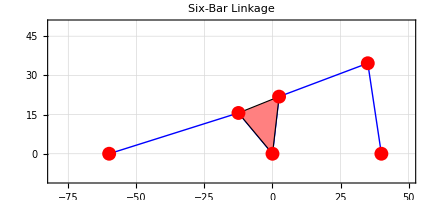

```mathematica
Show[{la1,la2,la3},PlotLabel -> "Six-Bar Linkage",PlotRange->{{-80,50},{-10,50}},Frame->True,GridLines->Automatic]
```

# 2. Animation

## 2.1 Input set of r2

```mathematica
nump=101;
```

```mathematica
R2={69,35};(* 設定動畫中二桿的位置*)
```

```mathematica
RSet2=Table[R2[[1]]+(R2[[2]]-R2[[1]])/(nump-1)*(k-1),{k,1,nump}]//N;
```

## 2.2 All angles

### Angle 1

```mathematica
AngSet1=Table[vtheta1,{k,1,nump}];
```

### Angle 2

```mathematica
AngSet2=Table[vtheta2,{k,1,nump}];
```

### Angle 3

```mathematica
AngSet3=Table[vtheta3/.{Subscript[l, 2]-> RSet2[[k]]},{k,1,nump}];
```

### Angle 4

```mathematica
AngSet4=Table[vtheta4/.{Subscript[l, 2]-> RSet2[[k]]},{k,1,nump}];
```

### Angle 6

```mathematica
AngSet6=Table[theta6/.{Subscript[θ, 1]->AngSet1[[k]],Subscript[θ, 2]->AngSet2[[k]],Subscript[θ, 4]->AngSet4[[k]] },{k,1,nump}];
```

### Angle 5

```mathematica
AngSet5=Table[theta5/.{Subscript[θ, 1]->AngSet1[[k]] ,Subscript[θ, 6]->AngSet6[[k]],Subscript[θ, 4]->AngSet4[[k]]},{k,1,nump}];
```

### Angle 7

```mathematica
AngSet7=Table[AngSet4[[k]] + π/4,{k,1,nump}];
```

### Allang

```mathematica
AllAngSet=Table[{Subscript[θ, 1]->AngSet1[[k]] ,Subscript[θ, 2]-> AngSet2[[k]],Subscript[θ, 3]-> AngSet3[[k]],Subscript[θ, 4]-> AngSet4[[k]],Subscript[θ, 7]-> AngSet7[[k]],Subscript[θ, 8]-> AngSet8[[k]]},{k,1,nump}];
```

```mathematica
AllAngSet[[1]];
```

## 2.3 All positions

```mathematica
AllPosi1=Table[{vrA,vrB,vrC,vrD,vrE,vrF}/.{Subscript[l, 2]-> RSet2[[k]]},{k,1,nump}];
```

```mathematica
AllPosi2=Table[{vrB,vrC,vrD}/.{Subscript[l, 2]-> RSet2[[k]]},{k,1,nump}];
```

```mathematica
AllPosi3=Table[{vrA,vrB,vrC,vrD,vrE,vrF}/.{Subscript[l, 2]-> RSet2[[k]]},{k,1,nump}];
```

## 2.4 Plot All positions

```mathematica
laSet1=Table[Graphics[{Blue,Thick,Line[AllPosi1[[k]]]}],{k,1,nump}];
```

```mathematica
laSet2=Table[Graphics[{EdgeForm[{Black,Thick}],Pink,Polygon[AllPosi2[[k]]]}],{k,1,nump}];
```

```mathematica
laSet3=Table[Graphics[{Red,PointSize[0.025],Point[AllPosi3[[k]]]}],{k,1,nump}];
```

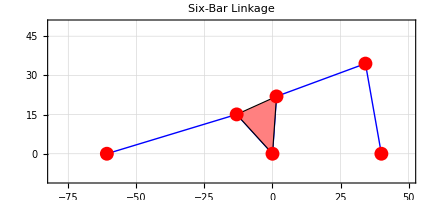

```mathematica
k=25;
Show[{laSet1[[k]],laSet2[[k]],laSet3[[k]]},PlotLabel -> "Six-Bar Linkage",PlotRange->{{-80,50},{-10,50}},Frame->True,GridLines->Automatic]
```

## 2.5 Animate

```mathematica
Animate[Show[{laSet1[[k]],laSet2[[k]],laSet3[[k]]},PlotLabel -> "Six-Bar Linkage",PlotRange->{{-80,50},{-10,50}},Frame->True,GridLines->Automatic],{k,1,nump,1},AnimationRunning->False]
```